# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1;
```

```mathematica
ClearAll;
sysSTR="mul_helion_miwchan-v23";

ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/"<>sysSTR<>"/results";
files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]];

wrkDirs = "/home/kirscher/kette_repo/ComptonLIT/systems/"<>sysSTR<>"-"<>ToString[#]&/@Range[0,anzBas-1];
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v23/results
in
float32=Real32
format for
N_bases=4
evolved bases for the expansion of the final state.

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=He3NormHamMat[[Range[1,Length[He3NormHamMat],2]]];
ActiveBasVHe3=ReadList["../he3/basis_struct/Ssigbasv3heLIT_J0.5_npp0.5^+.dat"];

BareDims=ReadList["./BareBasDims_"<>ToString[#]<>".dat"]&/@Range[0,anzBas-1];
(*He3NormHamMat=tmp;*)
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
Print["N_(helion - full) = ",He3BasisDim];
Print["N_(helion - active) = ",Length[ActiveBasVHe3]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
MinMax[Eigenvalues[He3Norm]]
```

N_(helion - full) = 54

N_(helion - active) = 46

{0.0000429676,9.57226}

```mathematica
dg=Table[He3Norm[[i,i]],{i,1,Length[He3Norm]}];Take[dg,4]
SymmetricMatrixQ[He3Norm]
```

{1.,1.,1.,1.}

True

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {0.0000429676,9.57226}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -8.13632

Dim_full^helion = 54=^!54   ;     Dim_(non - singular)^helion = 54

Norm=1.

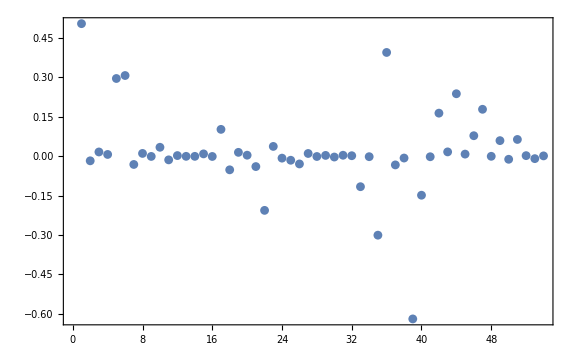
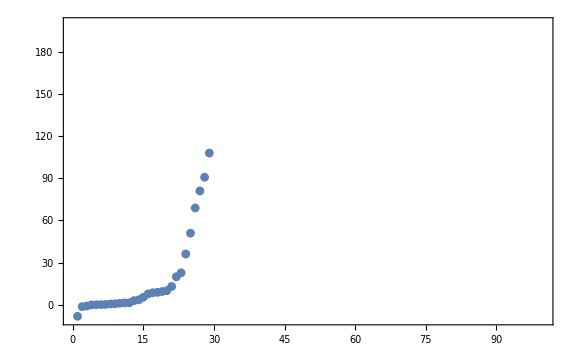
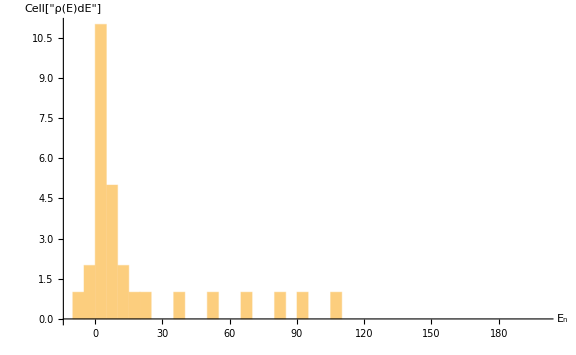
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}]

LitNormHamMat=Table[readREAL8list[#]&/@matnamesJ[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

ActiveBasVFin=ReadList[#<>"/basis_struct/Ssigbasv3heLIT_J0.5_0.5^-.dat"]&/@wrkDirs;

LITbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - full) = ",LITbasisDim];
LitNorm=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[1;;LITbasisDim[[Inn]][[#]]^2]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
LitHam=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[LITbasisDim[[Inn]][[#]]^2+1;;]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

LITbasisDim=Dimensions[LitNorm][[2]];
Print["N_(final - active) = ",Length[#]&/@ActiveBasVFin];
Print["min/max Norm EV = ",Table[MinMax[Eigenvalues[LitNorm[[Inn]][[#]]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}]];
```

{{mat_0.5^-_BasNR-0,mat_0.5^-_BasNR-1,mat_0.5^-_BasNR-2,mat_0.5^-_BasNR-3}}

N_(final - full) = {{45,46,51,49}}

N_(final - active) = {47,48,48,48}

min/max Norm EV = {{{0.0136832,3.4194},{0.0235763,3.85512},{0.00588552,5.43301},{0.01136,4.04965}}}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

```mathematica
dE=2.;
plts={};
Do[
Do[
Print["=== I_n=",Subscript[I, n][[nj]],"  BasNR: ",nb," ==="];
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[nb]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]][[nb]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]][[nb]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]][[nb]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];

plt1=ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large];

plt2=ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,40},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large];
plt3=Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,100},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}];
AppendTo[plts,{plt1,plt2,plt3}];
Print["==="];
,{nb,Range[anzBas]}];
,{nj,Range[1,Length[Subscript[I, n]]]}];
```

=== I_n=0.5  BasNR: 1 ===

Final-state Basis dimension = {45,45}

min/max: {0.0136832,3.4194}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.709368,0.0058639,0.00646463,0.00948193,0.0111432}

===

=== I_n=0.5  BasNR: 2 ===

Final-state Basis dimension = {46,46}

min/max: {0.0235763,3.85512}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.878541,-0.692016,0.00613659,0.00635726,0.00815412}

===

=== I_n=0.5  BasNR: 3 ===

Final-state Basis dimension = {51,51}

min/max: {0.00588552,5.43301}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.23863,-0.697018,0.00612028,0.00635726,0.00814829}

===

=== I_n=0.5  BasNR: 4 ===

Final-state Basis dimension = {49,49}

min/max: {0.01136,4.04965}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.525289,-0.134971,0.0058597,0.00645921,0.00834287}

===

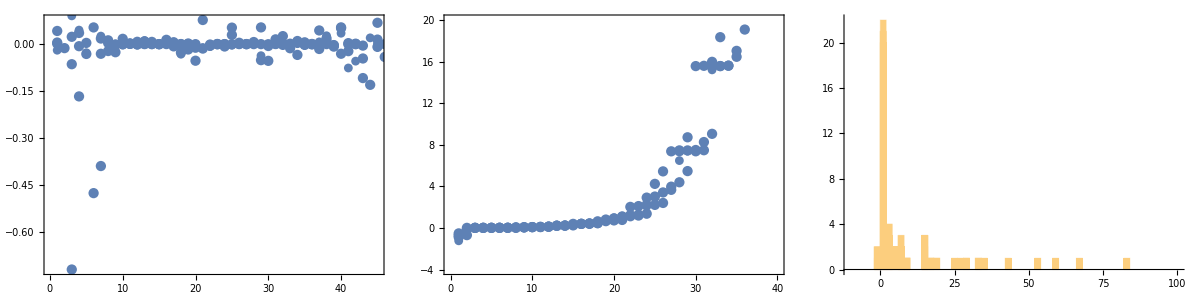

```mathematica
Grid[{{
Show[plts[[All,1]]],
Show[plts[[All,2]]],
Show[plts[[All,3]]]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockjs={};
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockj={};
CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockT={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb-1]<>"."<>dt;
tmp =BinaryReadList[fntmp,"Real32"];
OutDim=Dimensions[tmp][[1]]/BareDims[[nb]][[1]];
Print[Dimensions[tmp][[1]]];
test=ArrayReshape[tmp,{OutDim,BareDims[[nb]][[1]]}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockT,{mIn,test}];
AppendTo[CouplingBlockTA,{mIn,test[[ActiveBasVFin[[nb]],ActiveBasVHe3]]}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjs,CouplingBlockj];
AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim_active(⟨ψ|ο̂|helion⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim_bare(⟨ψ|ο̂|helion⟩)   = ",Table[Dimensions[CouplingBlockjs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam[[1]][[#]]]&/@Range[anzBas]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm[[1]][[#]]]&/@Range[anzBas]];
```

2744

Part::partw: Part 50 of {{-0.0161523,-0.0824854,-0.0407231,-0.00906807,-0.239384,-0.449114,-0.163965,-0.03467,-0.337111,-0.259653,-0.0747982,-0.0167234,-0.0658522,-0.0368932,«23»,-0.0201378,-0.0123551,-0.0110236,-0.0460221,-0.00415412,-0.00555043,-0.000858637,-0.231303,-0.16835,-0.027649,-0.0966375,0.0351317,0.00246119,«6»},«47»,{«1»}} does not exist.

2744

Part::partw: Part 50 of {{-0.0161523,-0.0824854,-0.0407231,-0.00906807,-0.239384,-0.449114,-0.163965,-0.03467,-0.337111,-0.259653,-0.0747982,-0.0167234,-0.0658522,-0.0368932,«23»,-0.0201378,-0.0123551,-0.0110236,-0.0460221,-0.00415412,-0.00555043,-0.000858637,-0.231303,-0.16835,-0.027649,-0.0966375,0.0351317,0.00246119,«6»},«47»,{«1»}} does not exist.

2688

Part::partw: Part 49 of {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,-0.0595686,«23»,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743,0.0213925,0.0017576,«6»},«46»,{-«20»,«49»,«6»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

2688

3136

3136

2744

2744

Dim_active(⟨ψ|ο̂|helion⟩) = {{{3},{3},{48,46},{48,46}}}

Dim_bare(⟨ψ|ο̂|helion⟩)   = {{{49,56},{48,56},{56,56},{49,56}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{45,45},{46,46},{51,51},{49,49}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{45,45},{46,46},{51,51},{49,49}}

Part::partw: Part {3,4,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50} of {{-0.0161523,-0.0824854,-0.0407231,-0.00906807,-0.239384,-0.449114,-0.163965,-0.03467,-0.337111,-0.259653,-0.0747982,-0.0167234,-0.0658522,-0.0368932,«23»,-0.0201378,-0.0123551,-0.0110236,-0.0460221,-0.00415412,-0.00555043,-0.000858637,-0.231303,-0.16835,-0.027649,-0.0966375,0.0351317,0.00246119,«6»},«47»,{«1»}} does not exist.

MatrixPlot::mat0: Argument «1» at position 1 is not a matrix.

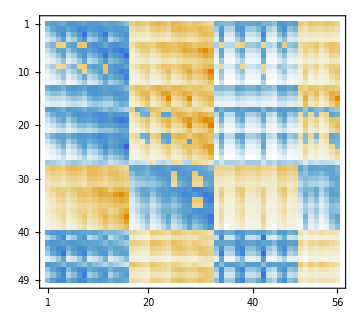
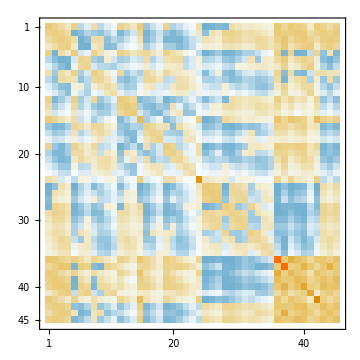
-Graphics- | MatrixPlot[{{-0.0161523,-0.0824854,-0.0407231,-0.00906807,-0.239384,-0.449114,-0.163965,-0.03467,-0.337111,-0.259653,-0.0747982,-0.0167234,-0.0658522,-0.0368932,-0.00741874,-0.00161771,0.0192339,0.0897032,0.0418374,0.00922722,0.255962,0.453666,0.157947,0.0331246,0.347985,0.244543,0.0699557,0.0153832,0.0666319,0.0341892,0.00677247,0.00150073,-0.00653801,-0.00448055,-0.0024074,-0.00274534,-0.0697361,-0.0201378,-0.0123551,-0.0110236,-0.0460221,-0.00415412,-0.00555043,-0.000858637,-0.231303,-0.16835,-0.027649,-0.0966375,0.0351317,0.00246119,0.0626508,0.0274666,0.0254305,0.0607205,0.029374,0.00588215},{-0.000578381,-0.0242295,-0.305116,-0.30212,-0.0124712,-0.217252,-1.60974,-0.95953,-0.129494,-0.398826,-0.886696,-0.374802,-0.0691103,-0.222116,-0.160889,-0.0482254,0.000521579,0.0034237,0.00199515,0.000457873,0.0154607,0.0443979,0.0192163,0.00416699,0.219145,0.535088,0.25062,0.0592972,0.137715,0.433839,0.161578,0.0392169,-0.000234511,-0.14962,-0.000068331,-0.0000796693,-0.0992995,-0.394162,-0.000410835,-0.000354601,-0.00330519,-0.166334,-0.000153871,-0.0000206007,-0.0305347,-0.597943,-0.000831974,-0.00399898,0.00106968,0.000117611,0.00235874,0.00127371,0.00071822,0.00245221,0.00167714,0.00033888},{-0.0000153426,-0.000783768,-0.0331772,-0.713751,-0.000340194,-0.00804566,-0.33193,-4.83428,-0.00485709,-0.0208376,-0.363313,-3.36854,-0.00368638,-0.0449903,-0.208029,-0.567762,0.0000136043,0.0000912315,0.0000540073,0.0000124311,0.000426289,0.00127923,0.000566625,0.000123332,0.00849432,0.03159,0.0193532,0.0048018,0.00791998,0.129148,0.29792,0.118194,-6.21814×10^-6,-0.31209,-1.78683×10^-6,-2.08599×10^-6,-0.00449992,-0.156961,-0.0000108477,-9.34389×10^-6,-0.0000920493,-1.4594,-4.01865×10^-6,-5.3361×10^-7,-0.000907754,-0.042331,-0.0000218425,-0.000107176,0.0000280938,3.18414×10^-6,0.000062796,0.0000344075,0.000018778,0.0000655962,0.0000460324,9.30794×10^-6},{-3.99827×10^-7,-0.0000206553,-0.000960569,-0.0413292,-8.87906×10^-6,-0.00021381,-0.0103486,-0.432555,-0.000129204,-0.00056709,-0.0127522,-0.542053,-0.00010048,-0.00142854,-0.00978051,-0.17701,3.54203×10^-7,2.37808×10^-6,1.40899×10^-6,3.24367×10^-7,0.0000111327,0.0000334898,0.0000148535,3.23371×10^-6,0.000226375,0.000867048,0.000542885,0.000135255,0.000216946,0.00424584,0.0155458,0.00770404,-1.62041×10^-7,-0.0171176,-4.65287×10^-8,-5.43225×10^-8,-0.000121158,-0.00541842,-2.8262×10^-7,-2.43413×10^-7,-2.40521×10^-6,-0.21476,-1.04638×10^-7,-1.3888×10^-8,-0.0000238068,-0.00117869,-5.68897×10^-7,-2.79457×10^-6,7.31728×10^-7,8.30712×10^-8,1.63679×10^-6,8.97552×10^-7,4.88969×10^-7,1.71022×10^-6,1.20185×10^-6,2.43029×10^-7},{-0.000385065,-0.0033884,0.0126282,0.00854806,-0.0128451,-0.049967,0.0736488,0.038474,-0.189858,-0.601634,-0.20595,-0.0148534,-0.247774,-0.603532,-0.208413,-0.0486103,0.000534363,0.0144821,0.0658465,0.0299891,0.0135364,0.167809,0.425755,0.147777,0.113975,0.47387,0.831744,0.295646,0.0481145,0.176644,0.173763,0.0572099,-0.00014774,0.00417386,-0.0000489929,-0.0000564407,0.00101532,0.0135307,-0.000283802,-0.0002494,-0.00144537,0.0043452,-0.000116991,-0.0000165589,-0.0119296,0.0211018,-0.00072354,-0.00320017,0.00187631,0.00857022,0.0113122,0.0458073,0.00092504,0.0192686,0.090141,0.021647},{-0.0000137788,-0.000546408,-0.0136896,-0.0452215,-0.000543592,-0.0106286,-0.183367,-0.307055,-0.0488554,-0.277541,-1.71603,-1.54464,-0.421466,-1.83688,-3.37427,-1.6164,0.0000170664,0.00065789,0.0129853,0.0263284,0.000614348,0.0124921,0.156331,0.167425,0.0530448,0.311462,1.4827,0.935833,0.475821,2.14174,3.42031,1.40145,-5.29607×10^-6,-0.0209733,-1.58726×10^-6,-1.84542×10^-6,-0.00267791,-0.0327756,-9.82801×10^-6,-8.51325×10^-6,-0.0000741531,-0.0325867,-3.75235×10^-6,-5.01671×10^-7,-0.000887165,-0.0260249,-0.0000240119,-0.000121633,0.0000653749,0.00980237,0.000527785,0.00979654,0.000030395,0.00110909,0.0617056,0.0266191},{-3.15286×10^-7,-0.0000137179,-0.000665412,-0.0248568,-0.0000125686,-0.000280785,-0.0131534,-0.387219,-0.00144731,-0.00845902,-0.184143,-4.03221,-0.0522188,-0.241147,-0.896433,-6.4433,3.88021×10^-7,0.000015277,0.00034421,0.000908351,0.000014265,0.000300563,0.00452484,0.00617823,0.0015992,0.0100526,0.063176,0.0507828,0.0598732,0.343797,1.24607,0.895641,-1.21185×10^-7,-0.0101694,-3.61157×10^-8,-4.20111×10^-8,-0.0000797825,-0.00380182,-2.24466×10^-7,-1.94279×10^-7,-1.73298×10^-6,-0.0844635,-8.53336×10^-8,-1.13729×10^-8,-0.0000212935,-0.000980139,-5.47138×10^-7,-2.79342×10^-6,1.4937×10^-6,0.000362691,0.000012277,0.000262323,6.92156×10^-7,0.0000261719,0.00200918,0.00100567},{-8.27511×10^-9,-3.61869×10^-7,-0.0000182707,-0.000916475,-3.30066×10^-7,-7.42858×10^-6,-0.000371893,-0.0176721,-0.00003856,-0.000225737,-0.00544154,-0.254897,-0.00157054,-0.00739522,-0.0300493,-0.632899,1.01806×10^-8,4.01286×10^-7,9.1087×10^-6,0.0000244261,3.74703×10^-7,7.91036×10^-6,0.000120358,0.000166868,0.0000426423,0.000269179,0.00172316,0.00141021,0.00179997,0.0106401,0.043708,0.0353702,-3.18067×10^-9,-0.000365713,-9.47618×10^-10,-1.10234×10^-9,-2.12496×10^-6,-0.000112054,-5.89082×10^-9,-5.09839×10^-9,-4.55364×10^-8,-0.00506745,-2.23895×10^-9,-2.98348×10^-10,-5.60335×10^-7,-0.0000264755,-1.43571×10^-8,-7.33316×10^-8,3.92012×10^-8,9.79765×10^-6,3.22516×10^-7,6.9458×10^-6,1.81619×10^-8,6.88069×10^-7,0.0000538298,0.0000272047},{-8.79669×10^-6,-0.000193733,0.000658245,0.00242562,-0.000332846,-0.00312054,0.00943547,0.0147808,-0.0124863,-0.067547,-0.0162798,0.0628165,-0.0668668,-0.473858,-0.337912,-0.0375234,0.0000114602,0.000421009,0.006324,0.00829358,0.000365106,0.00686379,0.0632109,0.0489947,0.0106095,0.0580905,0.311396,0.239708,0.0109231,0.0536783,0.220755,0.416817,-3.37457×10^-6,0.00114524,-1.0494×10^-6,-1.21603×10^-6,-0.000305984,0.00218393,-6.34994×10^-6,-5.52957×10^-6,-0.0000413113,0.00150807,-2.49307×10^-6,-3.40022×10^-7,-0.000426126,-0.000156529,-0.0000158409,-0.0000765291,0.0000435373,0.00279902,0.000337233,0.00468603,0.0000203834,0.000686402,0.0211819,0.00742539},{-2.48262×10^-7,-0.0000102122,-0.000331046,-0.00120382,-0.0000100678,-0.00021016,-0.00527799,0.00208015,-0.00122365,-0.00798622,-0.086958,0.0945659,-0.0560941,-0.330321,-1.76226,-1.27535,3.0944×10^-7,0.0000131884,0.000533785,0.0115653,0.0000113641,0.000270322,0.00987119,0.143543,0.00129866,0.00882144,0.164104,1.41525,0.0597962,0.304273,1.60421,6.29362,-9.52667×10^-8,-0.000610482,-2.84879×10^-8,-3.31282×10^-8,-0.0000535417,-0.00104506,-1.76921×10^-7,-1.532×10^-7,-1.34723×10^-6,0.00237908,-6.74229×10^-8,-8.99684×10^-9,-0.0000164646,-0.000577105,-4.3421×10^-7,-2.21357×10^-6,1.21701×10^-6,0.0152525,0.0000106988,0.000430332,5.5656×10^-7,0.0000241231,0.012776,0.0623847},{-7.12049×10^-9,-3.03641×10^-7,-0.0000133875,-0.00054492,-2.899×10^-7,-6.37579×10^-6,-0.000266877,-0.0100022,-0.0000390168,-0.000256568,-0.00546346,-0.173932,-0.00577081,-0.0299305,-0.185452,-2.52136,8.85369×10^-9,3.80513×10^-7,0.0000165439,0.000595571,3.27756×10^-7,7.90889×10^-6,0.000325742,0.0100455,0.0000417184,0.00029016,0.00654438,0.155159,0.00617885,0.0322984,0.210695,2.16297,-2.73239×10^-9,-0.000219145,-8.15333×10^-10,-9.48321×10^-10,-1.70901×10^-6,-0.0000742869,-5.07075×10^-9,-4.38954×10^-9,-3.89528×10^-8,-0.00255036,-1.92927×10^-9,-2.57134×10^-10,-4.80951×10^-7,-0.0000204882,-1.24339×10^-8,-6.35763×10^-8,3.48874×10^-8,0.00157058,3.08909×10^-7,0.0000134397,1.5934×10^-8,7.00777×10^-7,0.000524228,0.00946733},{-1.66866×10^-10,-7.12948×10^-9,-3.19718×10^-7,-0.0000149884,-6.79515×10^-9,-1.49868×10^-7,-6.45739×10^-6,-0.000305576,-9.19688×10^-7,-6.05015×10^-6,-0.000134373,-0.00623949,-0.000148313,-0.000766024,-0.00478124,-0.109668,2.07457×10^-10,8.92004×10^-9,3.89338×10^-7,0.0000144611,7.68314×10^-9,1.8554×10^-7,7.6928×10^-6,0.000249452,9.83742×10^-7,6.85125×10^-6,0.000156291,0.00400504,0.000158609,0.000831168,0.0055365,0.0643144,0,-5.95495×10^-6,0,0,-4.02817×10^-8,-1.83369×10^-6,-1.18827×10^-10,-1.02862×10^-10,-9.1324×10^-10,-0.000089615,0,0,-1.1282×10^-8,-4.85753×10^-7,-2.91361×10^-10,-1.49×10^-9,8.17552×10^-10,0.0000403031,7.24178×10^-9,3.16417×10^-7,3.73372×10^-10,1.64337×10^-8,0.0000125415,0.000252621},{-0.0077101,-0.0482868,-0.0273361,-0.00623923,-0.160424,-0.373349,-0.15092,-0.0324161,-0.450486,-0.439618,-0.137037,-0.0309746,-0.107807,-0.0750055,-0.0158924,-0.00348869,0.0106164,0.110624,0.0908594,0.0222851,0.165958,0.589823,0.304771,0.0680938,0.392402,0.403774,0.140212,0.031736,0.0898294,0.065086,0.0144733,0.00325758,-0.00305318,-0.00302669,-0.00109093,-0.00124771,-0.0444436,-0.0137373,-0.0058329,-0.005182,-0.0237716,-0.00286091,-0.00255783,-0.000386275,-0.142797,-0.123715,-0.0142064,-0.0527135,0.0278651,0.00607612,0.0812136,0.0608518,0.0165185,0.0936791,0.0674656,0.0138265},{-0.000194898,-0.00146233,-0.000949099,-0.000222375,-0.00646512,-0.0205871,-0.00980762,-0.00216348,-0.10253,-0.342479,-0.194964,-0.0485446,-0.0719496,-0.461432,-0.289081,-0.0760509,0.000327011,0.0149937,0.286532,0.511596,0.00631271,0.141682,1.79956,1.74557,0.072722,0.262551,1.12882,0.690469,0.0476522,0.227396,0.244369,0.0911489,-0.0000751008,-0.000104327,-0.0000261993,-0.0000300338,-0.00146127,-0.000484654,-0.000146004,-0.00012925,-0.000642139,-0.000101976,-0.0000627541,-9.27591×10^-6,-0.0048526,-0.00512573,-0.000397506,-0.00157432,0.00144104,0.189502,0.0123865,0.219618,0.000631703,0.0262094,1.12343,0.453726},{-5.08246×10^-6,-0.0000385364,-0.0000252247,-5.92014×10^-6,-0.000173526,-0.000565351,-0.00027293,-0.0000603413,-0.00328233,-0.0139925,-0.0095969,-0.00247694,-0.00282651,-0.0530559,-0.183237,-0.0866349,8.62533×10^-6,0.000445664,0.019482,0.546921,0.000168805,0.00459228,0.201292,4.28826,0.00231884,0.0103239,0.232571,3.54427,0.00190451,0.0250389,0.131125,0.689077,-1.95547×10^-6,-2.77147×10^-6,-6.81279×10^-7,-7.81089×10^-7,-0.0000387035,-0.0000128941,-3.80534×10^-6,-3.36801×10^-6,-0.0000168085,-2.71485×10^-6,-1.63376×10^-6,-2.41207×10^-7,-0.000128794,-0.000137838,-0.0000104263,-0.0000414528,0.000039295,1.00891,0.000372923,0.016111,0.0000168816,0.000855906,0.492301,4.2703},{-1.34566×10^-7,-1.02089×10^-6,-6.68551×10^-7,-1.56921×10^-7,-4.60159×10^-6,-0.0000150108,-7.25199×10^-6,-1.60352×10^-6,-0.0000879153,-0.000380493,-0.000264289,-0.0000683872,-0.0000766653,-0.00157088,-0.00706145,-0.00389085,2.2851×10^-7,0.0000118855,0.000549807,0.0241027,4.47547×10^-6,0.000123093,0.00594325,0.256788,0.0000620991,0.000280066,0.00739615,0.330617,0.0000517254,0.000743895,0.00490277,0.113118,-5.177×10^-8,-7.34528×10^-8,-1.80352×10^-8,-2.06775×10^-8,-1.0256×10^-6,-3.41763×10^-7,-1.00749×10^-7,-8.91697×10^-8,-4.45123×10^-7,-7.19605×10^-8,-4.32524×10^-8,-6.38536×10^-9,-3.41327×10^-6,-3.65558×10^-6,-2.76139×10^-7,-1.0981×10^-6,1.04293×10^-6,0.0954137,9.95283×10^-6,0.000457536,4.4756×10^-7,0.0000229515,0.017584,0.69016},{-0.0756862,-0.114559,-0.0331684,-0.00680344,-0.113155,-0.118949,-0.0354555,-0.00728476,-0.0295345,-0.0168762,-0.00449554,-0.000994874,-0.00434565,-0.00194263,-0.000373289,-0.0000809425,0.0175661,-0.0158829,-0.0056703,-0.00118527,0.146899,0.0443001,0.00860988,0.00166094,0.066858,0.016583,0.0037625,0.000803325,0.00828044,0.00197779,0.000341863,0.000074511,-0.0413076,-0.00378637,-0.0203953,-0.0225628,-0.0686799,-0.0156045,-0.0639408,-0.0592049,-0.124095,-0.00311854,-0.0357602,-0.00722947,-0.189943,-0.080078,-0.0563618,-0.135758,-0.0106093,-0.000389825,-0.0142892,-0.00442321,-0.00191215,-0.0122784,-0.00156689,-0.000314603},{-0.000203219,-0.00670232,-0.0628714,-0.0484027,-0.00670297,-0.0993319,-0.509853,-0.253667,-0.133305,-0.604121,-1.40533,-0.590641,-0.090831,-0.352196,-0.393973,-0.135317,0.000234495,0.00388477,-0.00638272,-0.00956143,0.00775377,0.0550018,-0.0522006,-0.0448617,0.196024,0.776684,0.373533,0.043412,0.256617,0.970608,0.414554,0.101245,-0.0000788469,-0.0233697,-0.0000239116,-0.0000277709,-0.0242558,-0.069916,-0.00014563,-0.000126369,-0.00104761,-0.0255606,-0.0000561303,-7.57043×10^-6,-0.0112123,-0.158143,-0.000342298,-0.00168874,0.00070571,-0.00302635,0.00282575,-0.00520148,0.000380328,0.00342335,-0.0251786,-0.0076725},{-5.84322×10^-6,-0.000228065,-0.00515953,-0.013769,-0.000233809,-0.00448882,-0.0673667,-0.0927201,-0.0240632,-0.141558,-0.802308,-0.630098,-0.371531,-1.84211,-4.08108,-2.02499,7.30588×10^-6,0.000305568,0.0101696,0.0665549,0.000263181,0.00601709,0.15664,0.514799,0.0252867,0.151431,1.59769,2.66186,0.39817,1.66395,3.72338,2.65753,-2.2439×10^-6,-0.00641959,-6.7316×10^-7,-7.8258×10^-7,-0.00108628,-0.0111538,-4.16883×10^-6,-3.61162×10^-6,-0.000031331,-0.00937092,-1.59278×10^-6,-2.13019×10^-7,-0.000375345,-0.0102457,-0.000010233,-0.0000518158,0.0000286233,0.0360506,0.00024752,0.00801826,0.0000131259,0.000549944,0.115642,0.107097},{-1.39316×10^-7,-5.48973×10^-6,-0.000132231,-0.000406621,-5.63621×10^-6,-0.000109979,-0.00180653,-0.00284871,-0.000668461,-0.00406648,-0.0267831,-0.0244692,-0.025258,-0.147116,-0.613087,-0.516111,1.74962×10^-7,7.73367×10^-6,0.000385983,0.0160805,6.33424×10^-6,0.000157311,0.00771628,0.272106,0.000691794,0.00425773,0.109487,3.18755,0.0265581,0.121886,0.488406,5.86943,-5.34698×10^-8,-0.000188604,-1.60313×10^-8,-1.86381×10^-8,-0.0000265985,-0.000305365,-9.93706×10^-8,-8.6081×10^-8,-7.48627×10^-7,-0.000288054,-3.79483×10^-8,-5.07291×10^-9,-9.02624×10^-6,-0.000257582,-2.44503×10^-7,-1.23986×10^-6,6.95763×10^-7,0.0451209,6.305×10^-6,0.000316584,3.16137×10^-7,0.0000145623,0.0137241,0.281729},{-3.51089×10^-9,-1.38418×10^-7,-3.34559×10^-6,-0.0000103721,-1.42122×10^-7,-2.77567×10^-6,-0.0000458238,-0.000072837,-0.0000169903,-0.00010356,-0.000688294,-0.00063499,-0.000683649,-0.00403857,-0.0179809,-0.0162615,4.41026×10^-9,1.9553×10^-7,9.99272×10^-6,0.000499226,1.5971×10^-7,3.9845×10^-6,0.000203304,0.00969979,0.000017569,0.000108296,0.00296512,0.141601,0.000718069,0.00333477,0.014125,0.360211,-1.34745×10^-9,-4.80946×10^-6,-4.03977×10^-10,-4.69668×10^-10,-6.71278×10^-7,-7.75498×10^-6,-2.50419×10^-9,-2.16928×10^-9,-1.88683×10^-8,-7.36533×10^-6,-9.56293×10^-10,-1.27834×10^-10,-2.27575×10^-7,-6.51015×10^-6,-6.16241×10^-9,-3.12518×10^-8,1.75522×10^-8,0.00201915,1.59465×10^-7,8.21659×10^-6,7.97131×10^-9,3.69096×10^-7,0.000390102,0.0170281},{-0.000213366,-0.00698666,-0.0635802,-0.0476048,-0.00698025,-0.102412,-0.509267,-0.248466,-0.132238,-0.596226,-1.36783,-0.57078,-0.0868655,-0.336359,-0.375068,-0.128646,0.000245342,0.0039102,-0.00703296,-0.009557,0.0080837,0.0550291,-0.0554067,-0.0446895,0.197622,0.769535,0.356941,0.040193,0.257305,0.944535,0.394913,0.0961094,-0.0000828215,-0.0229983,-0.0000251291,-0.0000291836,-0.0250163,-0.0695386,-0.000152931,-0.000132715,-0.00109803,-0.0250353,-0.0000589673,-7.95605×10^-6,-0.0116958,-0.161064,-0.000358778,-0.00176806,0.00073004,-0.00300452,0.00283042,-0.0056402,0.000396159,0.0033341,-0.0253705,-0.00760747},{-4.15726×10^-6,-0.000164772,-0.00413494,-0.0140438,-0.000156329,-0.00304779,-0.0538,-0.096059,-0.00847311,-0.0483847,-0.3817,-0.515201,-0.0193263,-0.0959232,-0.409309,-0.907543,5.00559×10^-6,0.000144122,9.47838×10^-6,-0.00351321,0.000178751,0.00245674,-0.0053092,-0.0241279,0.0104698,0.0617612,0.0250025,-0.115034,0.0580559,0.554906,0.626525,0.0533567,-1.60184×10^-6,-0.00650712,-4.80105×10^-7,-5.5819×10^-7,-0.000807431,-0.00999198,-2.96588×10^-6,-2.56915×10^-6,-0.0000223726,-0.0102523,-1.13248×10^-6,-1.51453×10^-7,-0.000263492,-0.00774684,-7.14755×10^-6,-0.0000361581,0.0000176921,-0.00155036,0.000111565,-0.0000863048,8.64102×10^-6,0.000190973,-0.00678224,-0.0043513},{-1.13581×10^-7,-4.81963×10^-6,-0.000203578,-0.00593743,-4.60691×10^-6,-0.00010051,-0.0039118,-0.0869379,-0.000587237,-0.00382424,-0.0726079,-1.06856,-0.0446114,-0.229368,-1.27366,-7.12334,1.41041×10^-7,5.94873×10^-6,0.000220014,0.00240841,5.21078×10^-6,0.000122225,0.00383871,0.0179563,0.000631402,0.00435293,0.0669084,0.0928194,0.0489642,0.269269,1.54198,2.09669,-4.3593×10^-8,-0.00245379,-1.30118×10^-8,-1.51337×10^-8,-0.0000268639,-0.0010411,-8.0894×10^-8,-7.00297×10^-8,-6.20667×10^-7,-0.0170224,-3.07849×10^-8,-4.10388×10^-9,-7.64351×10^-6,-0.00031691,-1.98214×10^-7,-1.01287×10^-6,5.53008×10^-7,0.00047978,4.81849×10^-6,0.000175575,2.53353×10^-7,0.0000107815,0.0036795,-0.00278284},{-3.07466×10^-9,-1.30958×10^-7,-5.71415×10^-6,-0.000213769,-1.25231×10^-7,-2.74982×10^-6,-0.000113087,-0.0036988,-0.0000169104,-0.000111331,-0.00231596,-0.0597411,-0.00260922,-0.0136245,-0.0858439,-0.92923,3.82442×10^-9,1.64805×10^-7,7.3348×10^-6,0.000318843,1.4156×10^-7,3.42938×10^-6,0.000146973,0.0061443,0.0000180575,0.000125598,0.00300152,0.114111,0.00278418,0.0144234,0.0942863,1.75414,-1.17982×10^-9,-0.0000865778,-3.52079×10^-10,-4.09503×10^-10,-7.35346×10^-7,-0.0000310767,-2.18962×10^-9,-1.89548×10^-9,-1.68156×10^-8,-0.000873632,-8.33128×10^-10,-1.11044×10^-10,-2.07593×10^-7,-8.78574×10^-6,-5.37006×10^-9,-2.7456×10^-8,1.50808×10^-8,0.00118207,1.33837×10^-7,5.97419×10^-6,6.88475×10^-9,3.04213×10^-7,0.000256469,0.00914043},{-1.01934×10^-10,-4.34253×10^-9,-1.89812×10^-7,-7.20333×10^-6,-4.15269×10^-9,-9.12167×10^-8,-3.7626×10^-6,-0.000125951,-5.62519×10^-7,-3.7056×10^-6,-0.0000774843,-0.00207298,-0.0000908405,-0.000474889,-0.00302142,-0.0347489,1.26802×10^-10,5.47058×10^-9,2.45957×10^-7,0.0000116353,4.69404×10^-9,1.13914×10^-7,4.96741×10^-6,0.000238941,6.00456×10^-7,4.17844×10^-6,0.000102496,0.00490149,0.0000967697,0.000500143,0.00329505,0.0860286,0,-2.91385×10^-6,0,0,-2.43935×10^-8,-1.03582×10^-6,0,0,-5.5751×10^-10,-0.000030129,0,0,-6.88352×10^-9,-2.91648×10^-7,-1.78041×10^-10,-9.10314×10^-10,5.00169×10^-10,0.0000510967,4.44324×10^-9,2.0056×10^-7,2.28297×10^-10,1.01081×10^-8,8.98305×10^-6,0.000455934},{-0.000270781,-0.000210274,-0.0000512017,-0.0000102674,-0.000162558,-0.000463362,-0.000231589,-0.0000516889,-0.000040345,-0.000177088,-0.000468308,-0.000222714,-8.17081×10^-6,-0.0000402685,-0.000163566,-0.000317738,-5.52717×10^-6,-0.0000499206,-0.0000130719,-2.6408×10^-6,0.000268099,-0.0000249245,-0.000054838,-0.000013147,0.00120543,0.000296454,-0.0000227842,-0.0000508349,0.00563433,0.00113301,0.000262875,0.0000149119,-0.000195738,-5.04564×10^-6,-0.000144624,-0.000152607,-0.000110977,-0.0000234908,-0.000248816,-0.0002381,-0.000306425,-4.65965×10^-6,-0.000171592,-0.000047969,-0.000431915,-0.000218189,-0.000100752,-0.000260805,-0.0000493332,-6.91553×10^-7,-0.0000357976,-8.51247×10^-6,-0.0000483402,-0.0000276635,-8.77058×10^-6,-1.73906×10^-6},{0.0130536,0.0751006,0.0401535,0.00906948,0.21721,0.43015,0.163859,0.0348869,0.40685,0.308165,0.0896087,0.0200674,0.0830819,0.0461654,0.00932715,0.00203533,-0.0156162,-0.0773439,-0.0373341,-0.00828261,-0.225076,-0.470671,-0.172387,-0.0364145,-0.311287,-0.285643,-0.086794,-0.0192346,-0.0644687,-0.0412371,-0.00850316,-0.00189351,0.0052751,0.00449907,0.00190805,0.0021796,0.0667921,0.0200628,0.00993098,0.00884005,0.0389601,0.00416093,0.00440579,0.000677027,0.204355,0.162975,0.02304,0.0808975,-0.0289683,-0.00217422,-0.0535428,-0.0242176,-0.0207376,-0.0524618,-0.0276999,-0.0055551},{0.0013829,0.00998082,0.00631842,0.00147331,0.0340113,0.0781624,0.034057,0.00742156,0.344755,0.357519,0.115912,0.0262384,0.161809,0.210613,0.055827,0.0125296,-0.00174958,-0.0119925,-0.0111674,-0.00457704,-0.0313135,-0.172838,-0.261863,-0.106433,0.0244351,-0.252224,-0.316525,-0.105687,0.0339528,-0.042607,-0.0471271,-0.0138754,0.000552499,0.000722579,0.000193787,0.000222014,0.00985281,0.00322607,0.0010414,0.000923187,0.00448993,0.000677305,0.000451991,0.0000686673,0.0272032,0.0269744,0.00271027,0.00960888,-0.00356242,-0.000866767,-0.00802352,-0.00614744,-0.00240638,-0.00860032,-0.0269503,-0.00708009},{0.00015496,0.00113362,0.000725552,0.000169547,0.00390967,0.00909113,0.00400859,0.00087544,0.0487471,0.0584215,0.0194992,0.00438073,0.0287746,0.0917222,0.0605975,0.0149407,-0.000196698,-0.00138701,-0.00192123,-0.00463164,-0.00356894,-0.0221487,-0.0798414,-0.221848,0.00607656,-0.0376832,-0.139704,-0.300017,0.00868282,0.0128403,-0.0392253,-0.0526274,0.0000618693,0.0000830592,0.0000216635,0.0000248229,0.00112655,0.000370986,0.000116626,0.000103364,0.000505569,0.0000779526,0.0000505563,7.67574×10^-6,0.00309154,0.00311306,0.000305568,0.00108404,-0.000402901,-0.00179983,-0.000924621,-0.00101918,-0.000271128,-0.00100777,-0.018574,-0.028345},{0.0000177365,0.000129847,0.0000831557,0.0000194341,0.000448116,0.00104268,0.000460055,0.000100484,0.00565452,0.00684415,0.00228808,0.000513509,0.00338773,0.0117944,0.00951336,0.00238678,-0.0000225178,-0.000159038,-0.000227604,-0.000779208,-0.000408872,-0.00255479,-0.00993458,-0.0472218,0.000721439,-0.00438744,-0.018329,-0.086967,0.00104051,0.0020107,-0.00571834,-0.0207658,7.08121×10^-6,9.51996×10^-6,2.47925×10^-6,2.84085×10^-6,0.000129084,0.0000425221,0.0000133484,0.0000118303,0.0000578818,8.93527×10^-6,5.78603×10^-6,8.78438×10^-7,0.000354124,0.000356887,0.0000349864,0.000124123,-0.0000461386,-0.000523375,-0.000105997,-0.000120621,-0.0000310421,-0.00011565,-0.00267641,-0.0119851},{0.0000969699,0.00302137,0.0223511,0.0140584,0.00325083,0.0493647,0.204573,0.0888049,0.0514208,0.413126,1.29034,0.553533,0.0317917,0.310806,0.646833,0.250059,-0.000118028,-0.00354406,-0.0224528,-0.0125702,-0.00386978,-0.0484944,-0.170066,-0.0679592,-0.330983,-0.587039,-0.73245,-0.267371,-1.9361,-2.02553,-0.695615,-0.191112,0.0000374221,0.00673959,0.0000113903,0.0000132246,0.0100276,0.0219734,0.0000695316,0.0000603587,0.000493259,0.00720694,0.0000268406,3.60879×10^-6,0.00538569,0.063502,0.000162868,0.000819387,-0.000425112,-0.00367966,-0.002789,-0.0158176,-0.000205884,-0.00502702,-0.0370845,-0.00946731},{0.0000123614,0.000479827,0.0104868,0.026008,0.000490072,0.00926059,0.132134,0.169822,0.0474281,0.258019,1.27066,0.920395,0.561375,2.32495,3.46968,1.43907,-0.0000153588,-0.000593641,-0.0118956,-0.0248076,-0.000551132,-0.0113779,-0.146193,-0.161549,-0.0412839,-0.273569,-1.52991,-1.05716,-0.165957,-1.15892,-3.17464,-1.57829,4.75055×10^-6,0.0121634,1.42565×10^-6,1.65733×10^-6,0.00226379,0.021893,8.82089×10^-6,7.64235×10^-6,0.0000661963,0.0173574,3.37142×10^-6,4.51171×10^-7,0.000787879,0.0209711,0.0000216199,0.000109202,-0.0000588617,-0.0092956,-0.000476231,-0.00898183,-0.0000273571,-0.00100243,-0.0579063,-0.0253757},{1.23801×10^-6,0.0000486679,0.00115598,0.00344083,0.0000495641,0.000950351,0.0152424,0.0232921,0.00573677,0.0304155,0.165352,0.140805,0.202076,0.849119,1.42204,0.660385,-1.53996×10^-6,-0.0000604147,-0.00132752,-0.00333982,-0.0000555472,-0.00118825,-0.017636,-0.026897,-0.00391178,-0.0307925,-0.26591,-0.591217,0.0346477,0.0277155,-1.02025,-2.57776,4.75662×10^-7,0.00159977,1.42637×10^-7,1.65828×10^-7,0.000234929,0.00263005,8.83187×10^-7,7.65106×10^-7,6.6486×10^-6,0.00241474,3.37379×10^-7,4.51372×10^-8,0.0000795361,0.00224468,2.17015×10^-6,0.0000109639,-5.92243×10^-6,-0.00131868,-0.0000485194,-0.00100908,-2.74618×10^-6,-0.000103154,-0.0075198,-0.00399005},{1.28882×10^-7,5.07001×10^-6,0.000120982,0.000363985,5.16256×10^-6,0.0000990672,0.00159943,0.00246966,0.000603649,0.00319611,0.0174841,0.015054,0.0230929,0.0978297,0.168862,0.0795318,-1.60326×10^-7,-6.29489×10^-6,-0.000139034,-0.000354099,-5.78467×10^-6,-0.000123987,-0.00185639,-0.00301585,-0.00040571,-0.00322679,-0.0287947,-0.088909,0.00434229,0.00574129,-0.117077,-0.49913,4.95176×10^-8,0.000169168,1.48483×10^-8,1.72625×10^-8,0.0000245046,0.000276618,9.19419×10^-8,7.96489×10^-8,6.92253×10^-7,0.000256233,3.51209×10^-8,4.69868×10^-9,8.28359×10^-6,0.000234537,2.25948×10^-7,1.14154×10^-6,-6.16703×10^-7,-0.000140994,-5.05577×10^-6,-0.000105722,-2.85924×10^-7,-0.0000107546,-0.000795334,-0.000463867},{5.47795×10^-7,0.000021212,0.000454033,0.00107863,0.0000207879,0.000410013,0.00593227,0.00765631,0.000944834,0.00779328,0.0781549,0.0938658,0.0015795,0.0173952,0.279736,1.15685,-6.75569×10^-7,-0.0000259869,-0.000509808,-0.00101966,-0.0000240824,-0.0004572,-0.00593477,-0.00660086,-0.00342865,-0.0109985,-0.0507398,-0.0507437,-0.492082,-0.971857,-0.486506,-0.501353,2.10564×10^-7,0.000503109,6.31955×10^-8,7.34655×10^-8,0.0000994928,0.000928203,3.90881×10^-7,3.38639×10^-7,2.93297×10^-6,0.000711639,1.49325×10^-7,1.99408×10^-8,0.0000348802,0.000922729,9.41091×10^-7,4.80318×10^-6,-2.594×10^-6,-0.00037794,-0.0000209035,-0.0003849,-1.20538×10^-6,-0.000043891,-0.00239723,-0.00103018},{6.35417×10^-8,2.69257×10^-6,0.000112348,0.00300337,2.57777×10^-6,0.0000562402,0.00214577,0.041945,0.000322873,0.00214661,0.0408542,0.512316,0.0199835,0.109264,0.778943,4.97288,-7.89862×10^-8,-3.37488×10^-6,-0.000139599,-0.00348697,-2.91761×10^-6,-0.0000694713,-0.00262886,-0.0467276,-0.000374862,-0.00246697,-0.0464099,-0.515103,-0.0593689,-0.279401,-1.01637,-3.51763,2.43852×10^-8,0.00124921,7.27914×10^-9,8.46615×10^-9,0.0000149658,0.000561686,4.5256×10^-8,3.91783×10^-8,3.47122×10^-7,0.00774593,1.72232×10^-8,2.29586×10^-9,4.27606×10^-6,0.000175957,1.10881×10^-7,5.66814×10^-7,-3.10822×10^-7,-0.00540985,-2.73846×10^-6,-0.000112804,-1.42088×10^-7,-6.18611×10^-6,-0.00362372,-0.0238941},{7.46886×10^-9,3.18075×10^-7,0.0000138624,0.000513703,3.04124×10^-7,6.67472×10^-6,0.000273929,0.00882353,0.0000410055,0.000269145,0.00555826,0.139849,0.00621974,0.0322221,0.194341,1.9291,-9.28827×10^-9,-3.992×10^-7,-0.000017359,-0.000625661,-3.43766×10^-7,-8.29879×10^-6,-0.000341926,-0.0105654,-0.0000434232,-0.000303435,-0.00688845,-0.164261,-0.00571365,-0.0302995,-0.211612,-2.39067,2.86605×10^-9,0.000208225,8.55285×10^-10,9.94782×10^-10,1.78556×10^-6,0.0000752214,5.31897×10^-9,4.60447×10^-9,4.08464×10^-8,0.00206781,2.02384×10^-9,2.69752×10^-10,5.04161×10^-7,0.0000213208,1.30443×10^-8,6.66875×10^-8,-3.65999×10^-8,-0.00165334,-3.24078×10^-7,-0.0000141019,-1.67161×10^-8,-7.35198×10^-7,-0.000550423,-0.00998128},{7.54754×10^-10,3.21511×10^-8,1.4045×10^-6,0.0000530462,3.07389×10^-8,6.7485×10^-7,0.0000278058,0.000923583,4.16116×10^-6,0.0000272937,0.000566295,0.0149417,0.000670357,0.00346407,0.0207005,0.215485,-9.38632×10^-10,-4.03541×10^-8,-1.75952×10^-6,-0.0000648025,-3.47432×10^-8,-8.39346×10^-7,-0.0000347443,-0.00111154,-4.38433×10^-6,-0.0000307383,-0.000705573,-0.0178007,-0.000563461,-0.00301776,-0.0221956,-0.292262,2.89623×10^-10,0.0000214674,0,1.00524×10^-10,1.8058×10^-7,7.6558×10^-6,5.37497×10^-10,4.65294×10^-10,4.12791×10^-9,0.000220154,2.04512×10^-10,0,5.09555×10^-8,2.15805×10^-6,1.31823×10^-9,6.73933×10^-9,-3.69889×10^-9,-0.000177885,-3.27611×10^-8,-1.42979×10^-6,-1.6893×10^-9,-7.4338×10^-8,-0.0000564297,-0.00110309},{-0.0230639,-0.36793,-0.469217,-0.12847,-0.0195447,-0.0957998,-0.0734613,-0.0176927,-0.0160107,-0.0209694,-0.00861703,-0.00204469,-0.00349068,-0.00328758,-0.000819367,-0.000184345,0.00150737,0.000410758,0.0000832881,0.0000163384,0.0289903,0.0129316,0.00303143,0.000602933,0.0400686,0.0228977,0.00599945,0.00130368,0.00830033,0.00395228,0.000758889,0.00016748,-0.0254186,-0.163244,-0.00779541,-0.0090769,-0.577481,-0.282865,-0.0175786,-0.0152416,-0.107836,-0.0628766,-0.00658331,-0.0010008,-0.097295,-0.228969,-0.00583095,-0.0204207,0.000310625,2.53737×10^-6,0.000182945,0.0000367047,0.000584289,0.000133157,0.000128119,0.0000250642},{-0.0000186056,-0.00090491,-0.0395668,-1.30352,-0.0000191171,-0.000431055,-0.0197641,-0.536735,-0.0000395357,-0.000295406,-0.00602253,-0.130428,-0.000020104,-0.000549175,-0.00353379,-0.0248811,1.05999×10^-6,2.89876×10^-7,5.8804×10^-8,1.15361×10^-8,0.0000303779,0.0000158483,3.81197×10^-6,7.60509×10^-7,0.00012657,0.000472855,0.000233607,0.0000555835,0.000071919,0.0017673,0.00541345,0.00240588,-0.0000202528,-1.38705,-5.69995×10^-6,-6.68996×10^-6,-0.00541706,-0.220486,-0.0000137648,-0.0000117816,-0.000117232,-4.6017,-4.80181×10^-6,-6.8838×10^-7,-0.000157553,-0.00750187,-4.38657×10^-6,-0.000017857,2.14197×10^-7,1.75075×10^-9,1.26834×10^-7,2.54525×10^-8,4.04808×10^-7,9.23596×10^-8,9.82515×10^-8,1.92222×10^-8},{-0.060669,-0.374359,-0.196499,-0.044187,-0.127606,-0.239907,-0.0925467,-0.0197313,-0.0657573,-0.0426021,-0.0121966,-0.0027271,-0.0105991,-0.00530439,-0.00106013,-0.000231066,0.0154519,0.00753328,0.00166766,0.000330542,0.166626,0.0793416,0.0188547,0.00375635,0.120331,0.0422037,0.0101533,0.00218368,0.0178043,0.00542467,0.00097161,0.000212667,-0.03567,-0.0300555,-0.01216,-0.0140125,-0.336791,-0.0999927,-0.0465518,-0.0410857,-0.196707,-0.0206531,-0.0194216,-0.00301222,-0.312904,-0.25733,-0.0385373,-0.116643,0.00647038,0.0000703528,0.00422298,0.000920651,0.0093374,0.0031613,0.00168281,0.000329826},{-0.0023685,-0.095215,-1.20542,-1.24635,-0.00734063,-0.122825,-0.955788,-0.590197,-0.0163091,-0.0698654,-0.160666,-0.0697771,-0.00664602,-0.0342327,-0.0257579,-0.00781211,0.000453144,0.000228447,0.0000508647,0.0000100888,0.011,0.0070724,0.00177454,0.000355871,0.0456017,0.0984739,0.0381514,0.00874136,0.0205132,0.0731712,0.0260553,0.0062664,-0.00136297,-0.827695,-0.000383564,-0.000450187,-0.392712,-1.62748,-0.00170411,-0.00146185,-0.0138891,-0.703679,-0.000606482,-0.000082134,-0.0426387,-0.843097,-0.00129974,-0.00537727,0.000184957,2.03713×10^-6,0.000123114,0.0000269532,0.000267903,0.0000924006,0.0000616744,0.0000120918},{-0.000249418,-0.0118053,-0.416694,-4.05691,-0.000491206,-0.0106487,-0.343412,-1.83841,-0.00112177,-0.00745171,-0.0893721,-0.262694,-0.000552469,-0.0102813,-0.0319932,-0.0319051,0.0000289151,0.0000106955,2.26373×10^-6,4.46296×10^-7,0.00076097,0.000442749,0.000108769,0.0000217561,0.00341268,0.011675,0.0055498,0.00131235,0.00189538,0.0305062,0.0411508,0.013331,-0.000172816,-2.9883,-0.0000484611,-0.000056905,-0.0657817,-1.58363,-0.000180777,-0.000154825,-0.0015312,-4.73734,-0.0000635426,-8.71871×10^-6,-0.00349462,-0.144736,-0.0000978801,-0.000402757,8.6373×10^-6,8.11327×10^-8,5.32202×10^-6,1.11125×10^-6,0.0000141194,3.92533×10^-6,3.16591×10^-6,6.19982×10^-7},{-1.70866×10^-7,-8.33598×10^-6,-0.000378428,-0.0169591,-3.37991×10^-7,-7.70007×10^-6,-0.000376314,-0.0168725,-7.94555×10^-7,-5.74444×10^-6,-0.000130077,-0.00623454,-4.06648×10^-7,-0.0000114167,-0.0000874438,-0.001914,1.97533×10^-8,7.30784×10^-9,1.54676×10^-9,3.04945×10^-10,5.24435×10^-7,3.06349×10^-7,7.53149×10^-8,1.50658×10^-8,2.43351×10^-6,9.20932×10^-6,4.62351×10^-6,1.10317×10^-6,1.41568×10^-6,0.0000371582,0.000140377,0.0000695337,-1.18359×10^-7,-0.0112477,-3.313×10^-8,-3.8909×10^-8,-0.0000492659,-0.00221998,-1.23764×10^-7,-1.05967×10^-7,-1.05618×10^-6,-0.0979524,-4.34374×10^-8,-5.9529×10^-9,-2.43617×10^-6,-0.000118655,-6.69582×10^-8,-2.76405×10^-7,5.89864×10^-9,0,3.63503×10^-9,7.59015×10^-10,9.64316×10^-9,2.6811×10^-9,2.16694×10^-9,4.24354×10^-10},{-0.135535,-0.0570969,-0.0123388,-0.00243828,-0.0620521,-0.0188774,-0.00425419,-0.000843497,-0.00876189,-0.00181843,-0.000397902,-0.0000859435,-0.000876813,-0.000187619,-0.0000319761,-6.83495×10^-6,0.0912028,0.0288861,0.00597865,0.00117562,0.0603417,0.0165727,0.00362781,0.000715807,0.0086042,0.00166468,0.000368,0.0000783676,0.000844225,0.00017149,0.0000291255,6.33599×10^-6,-0.0977752,-0.00183954,-0.0830811,-0.0861588,-0.0284137,-0.00575754,-0.133918,-0.132957,-0.106444,-0.00113279,-0.118708,-0.0503331,-0.0616904,-0.0150073,-0.122746,-0.106006,0.0379756,0.00033882,0.0203263,0.00417621,0.057517,0.0147738,0.00251181,0.000491365},{-0.000715274,-0.0323182,-0.766178,-2.17976,-0.00314562,-0.0628742,-1.11606,-1.65436,-0.00882553,-0.046585,-0.258227,-0.224819,-0.00409413,-0.0406089,-0.0590671,-0.0261209,0.000185822,0.000123099,0.0000288589,5.76014×10^-6,0.00464328,0.00340208,0.000878574,0.000176827,0.0241791,0.0699328,0.0310928,0.00727616,0.0128456,0.104866,0.065599,0.0174928,-0.000374528,-1.29231,-0.000104277,-0.000122462,-0.159976,-1.73699,-0.000510292,-0.000437323,-0.00430026,-1.53233,-0.000181228,-0.0000242286,-0.0172169,-0.542431,-0.00047922,-0.00205195,0.0000957457,1.23076×10^-6,0.0000694372,0.0000159482,0.000126026,0.0000530824,0.0000321947,6.31985×10^-6},{-0.0000187359,-0.000918138,-0.0400455,-1.29107,-0.0000833841,-0.00190075,-0.0866015,-2.27453,-0.000254402,-0.00165534,-0.0335096,-0.691025,-0.000130918,-0.00315354,-0.0198309,-0.131392,4.83225×10^-6,3.20504×10^-6,7.51561×10^-7,1.50014×10^-7,0.00012361,0.0000916177,0.0000237174,4.77494×10^-6,0.000709167,0.00263295,0.00133513,0.000319187,0.000426529,0.0100279,0.0302675,0.0133798,-9.80464×10^-6,-0.674146,-2.71618×10^-6,-3.19134×10^-6,-0.00529356,-0.213843,-0.0000133433,-0.0000114266,-0.000114753,-4.27822,-4.71929×10^-6,-6.28856×10^-7,-0.000472637,-0.0224069,-0.0000125052,-0.0000540048,2.48898×10^-6,3.20123×10^-8,1.80619×10^-6,4.14919×10^-7,3.27606×10^-6,1.38091×10^-6,8.42393×10^-7,1.65365×10^-7},{-0.00176869,-0.0731082,-1.03437,-1.22534,-0.00767464,-0.133428,-1.19089,-0.820312,-0.0196766,-0.0850695,-0.223835,-0.105405,-0.00823689,-0.0458297,-0.0378202,-0.0119538,0.000463301,0.00030649,0.0000718327,0.0000143371,0.0112743,0.0081552,0.0021004,0.000422597,0.0529024,0.121078,0.048386,0.0111387,0.0248787,0.100917,0.0386807,0.00941567,-0.000926729,-0.743803,-0.000259497,-0.00030459,-0.310837,-1.49907,-0.00126433,-0.00108447,-0.0104134,-0.705271,-0.000451134,-0.0000605398,-0.040411,-0.870186,-0.00119012,-0.00504678,0.000238811,3.06787×10^-6,0.000173069,0.0000397417,0.000314349,0.000132291,0.0000797077,0.0000156465}}⟦{3,4,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,24,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}⟧,FrameLabel→{-Graphics-,-Graphics-},PlotLabel→-Graphics-,ImageSize→Medium]
-Graphics- | -Graphics-

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Medium]
},{
MatrixPlot[Chop[LitHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Medium,PlotLegends->Automatic]
}}]
```

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-8.13632 norm=1.

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
pltss={};
Do[
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]][[nb]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]][[nb]]).OμLHSEB;tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];AppendTo[pltss,ListPlot[inhomoEB[[1]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
Show[pltss]
```

Part::partw: Part {3,4,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50} of {{-0.0161523,-0.0824854,-0.0407231,-0.00906807,-0.239384,-0.449114,-0.163965,-0.03467,-0.337111,-0.259653,-0.0747982,-0.0167234,-0.0658522,-0.0368932,«23»,-0.0201378,-0.0123551,-0.0110236,-0.0460221,-0.00415412,-0.00555043,-0.000858637,-0.231303,-0.16835,-0.027649,-0.0966375,0.0351317,0.00246119,«6»},«47»,{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::dotsh: Tensors {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,«20»,-0.0016428,-0.114039,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743},«46»,{-0.0298924,-«21»,«43»,-«20»}} and {0.505054,-0.0176527,0.0160458,0.00658814,0.296043,0.307391,-0.0315667,0.010506,-0.000937899,0.0339271,-0.0140491,0.00229372,-0.000590673,-0.000642224,«23»,-0.00709272,-0.620236,-0.148807,-0.00216433,0.163961,0.0163484,0.237938,0.00788816,0.0779733,0.1787,-0.000480792,0.0592441,-0.0118413,«4»} have incompatible shapes.

Dot::dotsh: Tensors {{0.135077,-0.104774,0.0211947,-0.00268972,-0.00803067,0.00924935,-0.00318694,0.000585564,0.000675256,-0.00055436,0.000258254,-0.0000919623,0.0420626,-0.000914418,«23»,7.93344,0.000548209,2.66715,-0.584717,1.47819,0.520264,0.00179429,-0.00417909,-0.00810821,-2.86141,-8.70249,-2.93294,-0.0292367,«1»},«49»,«1»} and {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,«20»,-0.0016428,-0.114039,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743},«46»,{-0.0298924,-«21»,«43»,-«20»}} have incompatible shapes.

Dot::dotsh: Tensors {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,«20»,-0.0016428,-0.114039,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743},«46»,{-0.0298924,-«21»,«43»,-«20»}} and {0.505054,-0.0176527,0.0160458,0.00658814,0.296043,0.307391,-0.0315667,0.010506,-0.000937899,0.0339271,-0.0140491,0.00229372,-0.000590673,-0.000642224,«23»,-0.00709272,-0.620236,-0.148807,-0.00216433,0.163961,0.0163484,0.237938,0.00788816,0.0779733,0.1787,-0.000480792,0.0592441,-0.0118413,«4»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-8.13632

{1.,-8.13632}

```mathematica
CumStrengths={};pltsss={};
Do[
Do[
{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]][[nb]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]][[nb]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].EvecGSiEV);
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];

CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];

pl1=
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize];
pl2=
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]];

AppendTo[pltsss,{pl1,pl2}];
AppendTo[CumStrengths,CumStrengthsEV];

,{nb,Range[anzBas]}
]
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

E_0^initial = -8.13632    dim(initial) = {54}

E_0^final  = -0.709368    dim(final)   = {45}

Part::partw: Part {3,4,5,6,7,8,9,10,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50} of {{-0.0161523,-0.0824854,-0.0407231,-0.00906807,-0.239384,-0.449114,-0.163965,-0.03467,-0.337111,-0.259653,-0.0747982,-0.0167234,-0.0658522,-0.0368932,«23»,-0.0201378,-0.0123551,-0.0110236,-0.0460221,-0.00415412,-0.00555043,-0.000858637,-0.231303,-0.16835,-0.027649,-0.0966375,0.0351317,0.00246119,«6»},«47»,{«1»}} does not exist.

Transpose::nmtx: The first two levels of {{1699.93,1696.22,871.066,662.969,532.565,438.833,418.433,184.648,149.27,66.7352,52.3768,42.6316,18.3475,15.975,15.5928,«15»,0.395689,0.389733,0.23546,0.213915,0.120781,0.105439,0.0814325,0.0748282,0.0615691,0.0176318,0.0140325,0.0111432,0.00948193,0.00646463,0.0058639},2 («1»)^2} cannot be transposed.

Transpose::nmtx: The first two levels of {1699.93,1696.22,871.066,662.969,532.565,438.833,418.433,184.648,149.27,66.7352,52.3768,42.6316,18.3475,15.975,15.5928,«15»,0.395689,0.389733,0.23546,0.213915,0.120781,0.105439,0.0814325,0.0748282,0.0615691,0.0176318,0.0140325,0.0111432,0.00948193,0.00646463,0.0058639} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{1699.93,1696.22,871.066,662.969,532.565,438.833,418.433,184.648,149.27,66.7352,52.3768,42.6316,18.3475,15.975,15.5928,«15»,0.395689,0.389733,0.23546,0.213915,0.120781,0.105439,0.0814325,0.0748282,0.0615691,0.0176318,0.0140325,0.0111432,0.00948193,0.00646463,0.0058639}],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{1699.93,1696.22,871.066,662.969,532.565,438.833,418.433,184.648,149.27,66.7352,52.3768,42.6316,18.3475,15.975,15.5928,«15»,0.395689,0.389733,0.23546,0.213915,0.120781,0.105439,0.0814325,0.0748282,0.0615691,0.0176318,0.0140325,0.0111432,0.00948193,0.00646463,0.0058639},«1»}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

E_0^initial = -8.13632    dim(initial) = {54}

E_0^final  = -0.878541    dim(final)   = {46}

Part::partw: Part {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50} of {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,-0.0595686,«23»,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743,0.0213925,0.0017576,«6»},«46»,{-«20»,«49»,«6»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

E_0^initial = -8.13632    dim(initial) = {54}

E_0^final  = -1.23863    dim(final)   = {51}

Dot::dotsh: Tensors {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,«20»,-0.0016428,-0.114039,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743},«46»,{-0.0298924,-«21»,«43»,-«20»}} and {0.505054,-0.0176527,0.0160458,0.00658814,0.296043,0.307391,-0.0315667,0.010506,-0.000937899,0.0339271,-0.0140491,0.00229372,-0.000590673,-0.000642224,«23»,-0.00709272,-0.620236,-0.148807,-0.00216433,0.163961,0.0163484,0.237938,0.00788816,0.0779733,0.1787,-0.000480792,0.0592441,-0.0118413,«4»} have incompatible shapes.

Dot::dotsh: Tensors {{0.135077,-0.104774,0.0211947,-0.00268972,-0.00803067,0.00924935,-0.00318694,0.000585564,0.000675256,-0.00055436,0.000258254,-0.0000919623,0.0420626,-0.000914418,«23»,7.93344,0.000548209,2.66715,-0.584717,1.47819,0.520264,0.00179429,-0.00417909,-0.00810821,-2.86141,-8.70249,-2.93294,-0.0292367,«1»},«49»,«1»} and {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,«20»,-0.0016428,-0.114039,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743},«46»,{-0.0298924,-«21»,«43»,-«20»}} have incompatible shapes.

Dot::dotsh: Tensors {{-0.0104497,-0.100816,-0.0793639,-0.0193069,-0.175408,-0.552929,-0.276209,-0.061458,-0.369564,-0.378857,-0.126924,-0.029027,-0.0814534,«20»,-0.0016428,-0.114039,-0.0418306,-0.0077773,-0.00685357,-0.0379585,-0.00892444,-0.00326159,-0.000476927,-0.222424,-0.284408,-0.0167404,-0.0656743},«46»,{-0.0298924,-«21»,«43»,-«20»}} and {0.505054,-0.0176527,0.0160458,0.00658814,0.296043,0.307391,-0.0315667,0.010506,-0.000937899,0.0339271,-0.0140491,0.00229372,-0.000590673,-0.000642224,«23»,-0.00709272,-0.620236,-0.148807,-0.00216433,0.163961,0.0163484,0.237938,0.00788816,0.0779733,0.1787,-0.000480792,0.0592441,-0.0118413,«4»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

E_0^initial = -8.13632    dim(initial) = {54}

E_0^final  = -0.525289    dim(final)   = {49}

```mathematica
ListPlot[#->Range[Length[EvalsFEV]]&/@CumStrengths,Joined->False,ImageSize->ImgSize,PlotRange->{{-2.3,115},{0,0.1}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotStyle->PointSize[0.005]]
(*Put[CumStrengthsEV->Range[Length[EvalsFEV]],LocalObject["CumPlt_"<>sysSTR]]*)
```

Transpose::nmtx: The first two levels of {Transpose[{1699.93,1696.22,871.066,662.969,532.565,438.833,418.433,184.648,149.27,66.7352,52.3768,42.6316,18.3475,15.975,15.5928,«15»,0.395689,0.389733,0.23546,0.213915,0.120781,0.105439,0.0814325,0.0748282,0.0615691,0.0176318,0.0140325,0.0111432,0.00948193,0.00646463,0.0058639}],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{2376.2,2311.22,1813.71,1386.87,1197.81,478.013,434.265,384.038,35.6934,32.2083,28.0713,17.0301,15.6092,15.5678,15.4668,«16»,0.413649,0.389948,0.315962,0.226922,0.212087,0.132015,0.084465,0.0751895,0.0477607,0.0175159,0.0123968,0.0111842,0.00815412,0.00635726,0.00613659}],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {Transpose[{2668.11,2500.99,1921.56,1647.01,1386.97,1377.5,700.463,643.225,517.84,414.717,109.602,83.4269,59.2281,32.3196,29.8968,«21»,0.412189,0.389948,0.313223,0.226895,0.212086,0.127415,0.0843154,0.0751842,0.0473186,0.0174707,0.0123408,0.011182,0.00814829,0.00635726,«1»}],Transpose[«1»]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-